```mathematica
ClearAll["Global`*"]
```

# Severity Index Visualization

In this Notebook, we will create visualizations of the time-series data for several counties including their severity index. The purpose of these visualizations is the heuristically see the “goodness” of our severity index.

## Data Import

Here we will import the time-series data and the compiled data that will be used for the machine learning models.

## File Paths

```mathematica
hereDir=NotebookDirectory[];
projDir=ParentDirectory[hereDir];
compDataFile=FileNameJoin[{projDir,"RawDataToUsableDataConverter","src","FinalCombinedFeaturesWithSeverity.csv"}];
timeSeriesFile=FileNameJoin[{projDir,"RawDataToUsableDataConverter","src","StartingFiles","CovidFileWithDates.csv"}];
```

## Imported Data

The compiled data has information in the following order:
1. COVID Severity Index
2. FIPS County Code
3. Total Votes (2016)
4. Votes for Democratic Candidate (2008)
5. Votes for Democratic Candidate (2012)
6. Votes for Republican Candidate (2008)
7. Votes for Republican Candidate (2012)
8. Percentage of Votes for Democratic Candidate (2016)
9. Percentage of Votes for Republican Candidate (2016)
10. Percentage of Votes for Republican Candidate (2012)
11. Percentage of Votes for Republican Candidate (2008)
12. Percentage of Votes for Democratic Candidate (2012)
13. Percentage of Votes for Democratic Candidate (2008)
14. Percentage of Adults with Less Than a High School Diploma (Exit Poll 2016 Election)
15. Percentage of Adults with at Least a High School Diploma (Exit Poll 2016 Election)
16. Percentage of Adults with at Least a Bachelor’s Degree (Exit Poll 2016 Election)
17. Percentage of Adults with at Least a Graduate Degree (Exit Poll 2016 Election)
18. School Enrollment (???)
19. Percentage of Children Under 6 Living in Poverty (2016 Estimate)
20. Percentage of Adults 65 and Older Living in Poverty (2016 Estimate)
21. Total Population (2019 Estimate)
22. Poverty Rate Below Federal Poverty Threshold (2016 Estimate)
23. Percentage of People in Management, Professional, and Related Occupations (2016 Estimate)
24. Percentage of People in Service Occupations (2016 Estimate)
25. Percentage of People in Sales and Office Occupations (2016 Estimate)
26. Percentage of People in Farming, Fishing, and Forestry Occupations (2016 Estimate)
27. Percentage of People in Construction, Extraction, Maintenance, and Repair Occupations (2016 Estimate)
28. Percentage of People in Production, Transportation, and Material Moving Occupations (2016 Estimate)

The time-series data has entries in the following order:
1. Date (yyyy-mm-dd)
2. County Name
3. State Name
4. FIPS Code
5. Cumulative Number of Cases
6. Cumulative Number of Deaths

```mathematica
compData=Import[compDataFile,"Table","FieldSeparators"->";"];
timeSeriesData=Import[timeSeriesFile];
```

## Normalized Time - Series Data (Multiple Counties)

```mathematica
plotCountiesDataNormalized[fipsCodes_,timeSeriesData_,compData_,popIndex_]:=Module[{i,j,countyNames,countyStates,countySeverities,countyFips,timeSeriesCountyData,countyTimeSeries,plotLegends,countyFipsAndSeverity ,countyStartDate,countyEndDate,yearStartDateToEndDate,countyStartDateToEndDate,countyCases,pattern,countyData,countyPop,styleList},
countyNames=Table[0,{i,1,Length[fipsCodes],1}]; (* List of county names *)
countyStates = Table[0,{i,1,Length[fipsCodes],1}]; (* List of county states *)
countySeverities=Table[0,{i,1,Length[fipsCodes],1}]; (* List of county severity indicies *)
countyTimeSeries=Table[{},{i,1,Length[fipsCodes],1}]; (* List of county time-series *)
plotLegends=Table["",{i,1,Length[fipsCodes],1}]; (* List of County, State for plot legend *)

(* Here we sort the given counties by their severity index, greatest to least *)
countyFipsAndSeverity = Table[{0,0},{i,1,Length[fipsCodes],1}]; (* List of county FIPS codes and severity indices *)
For[i=1,i≤Length[fipsCodes],i++, (* Loop through each FIPs given to sort in order of descending severity index *)
countyFipsAndSeverity[[i,1]]=fipsCodes[[i]];
pattern=Table[_,{j,1,Length[compData[[1]]],1}];
pattern[[2]]=countyFipsAndSeverity[[i,1]];
countyData=Flatten[Cases[compData,pattern]];
countyFipsAndSeverity[[i,2]]=countyData[[1]];
];
countyFipsAndSeverity=Sort[countyFipsAndSeverity,#1[[2]]>#2[[2]]&];

(* Loop through each FIPs code given to pick out the time-series data and the severity index *)
For[i=1,i≤Length[fipsCodes],i++,
(* Pick out the time-series data *)
countyFips=countyFipsAndSeverity[[i,1]];
timeSeriesCountyData=Cases[timeSeriesData,{_,_,_,countyFips,_,_}];
countyNames[[i]]=timeSeriesCountyData[[1,2]];
countyStates[[i]]=timeSeriesCountyData[[1,3]];
countyStartDate=StringSplit[timeSeriesCountyData[[1,1]],"-"];
countyEndDate=StringSplit[timeSeriesCountyData[[-1,1]],"-"];
yearStartDateToEndDate=QuantityMagnitude[
DateDifference[{2020,01,01},ToExpression@countyEndDate]
]+1;
countyStartDateToEndDate=QuantityMagnitude[
DateDifference[ToExpression@countyStartDate,ToExpression@countyEndDate]
]+1;
countyCases=Flatten[{Table[0,{j,1,yearStartDateToEndDate-countyStartDateToEndDate,1}],timeSeriesCountyData[[;;,5]]}];

(* Pick out the county population, name, etc. *)
pattern=Table[_,{j,1,Length[compData[[1]]],1}];
pattern[[2]]=countyFips;
countyData=Flatten[Cases[compData,pattern]];
countySeverities[[i]]=countyData[[1]];
countyPop=countyData[[popIndex]];
countyTimeSeries[[i]]=countyCases/countyPop;
plotLegends[[i]]=StringJoin[countyNames[[i]], " County, ",countyStates[[i]], ": ", ToString[countySeverities[[i]]]];
];

styleList={Directive[Black,Thick],Directive[Black,Dashed,Thick],Directive[Black, DotDashed,Thick],Directive[Black,Dotted,Thick]}; (* List of plot styles to use in the plot *)

(* Return a plot of the time-series with severity index *)
Return[ListLinePlot[countyTimeSeries,
PlotRange->{0,Max[{Max[Flatten[countyTimeSeries]]},0.05]},
PlotLegends->plotLegends,
Axes->False,
Frame->{{True,False},{True,False}},
PlotLabel->StringJoin["Cumulative Cases per Capita in Various Counties"],
FrameLabel->{{"Cumulative  Cases per Capita",},{"Days from January 1^st, 2020",}},
PlotStyle->styleList,
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],
ImageSize->(72*6.5)
],Module]

]
```

## Example Severity Indices and Distribution of Severity Indices

## Severity Index Distribution

Generates the figure showing the distribution of severity indices, along with finding the county with maximal/minimal severity indexes.

```mathematica
(* Find the best-fit PDF *)
bestDist=FindDistribution[compData[[;;,1]],TargetFunctions->"Continuous"]
bestDistFunc[x_]:=PDF[bestDist,x]

(* Find the best-fit normal distribution *)
bestNormDistParams=FindDistributionParameters[compData[[;;,1]],NormalDistribution[μ,σ]]
bestNormDist[x_]:=PDF[NormalDistribution[μ,σ]/.bestNormDistParams,x]
```

MixtureDistribution[{0.928206,0.0717944},{NormalDistribution[-0.0813677,0.274586],LogNormalDistribution[0.0471292,0.722349]}]

{μ→0.0405684,σ→0.534157}

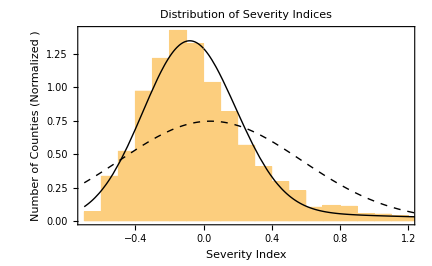

```mathematica
Show[
Histogram[compData[[;;,1]],Automatic,"PDF",
Frame->{{True,False},{True,False}},
Axes->False,
PlotLabel->"Distribution of Severity Indices",
FrameLabel->{{"Number of Counties (Normalized )",},{"Severity Index",}},
FrameStyle->Directive[Black],
FrameTicksStyle->Directive[Black],
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->16],
ImageSize->{6*72,Automatic}],
Plot[{bestDistFunc[x],bestNormDist[x]},{x,-0.7,1.4},
PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed,Thick]}]
]
```

```mathematica
MaximalBy[compData,First]
MinimalBy[compData,First]
```

{{6.99923,30011,778,111,96,573,678,87.018,8.99743,85.1759,79.3629,12.0603,15.374,8.9,91.1,15.2,4.4,76.,31.55,9.15,1252,12.65,0.45,59.9,11.15,13.,5.35,8.5,2.05}}

{{-0.67494,15007,26335,20416,18641,6245,6121,28.7602,62.4872,24.125,22.9393,73.4708,74.9927,11.7,88.3,22.7,6.8,73.45,11.45,9.55,72293,9.15,0.422,29.4,24.55,25.55,1.35,11.2,8.05}}

## Example Severity Indices

Generates the figure showing four example severity indices.

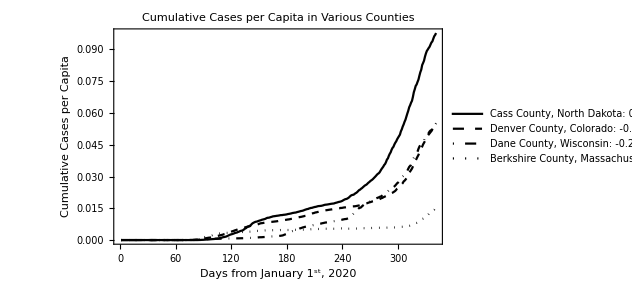

```mathematica
plotCountiesDataNormalized[{38017,08031,55025,25003},timeSeriesData,compData,21]
```

```mathematica
((3/4485414.)-Mean[{8/822083.,5/5150233.,4/3175692.,3/4485414.,3/10039107.}])/StandardDeviation[{8/822083.,5/5150233.,4/3175692.,3/4485414.,3/10039107.}]
```

-0.478028